# 16 Stability of Householder QR

The plan is to look at Householder QR with our new tool.

f̃ is backwards stable if  f̃(x)=f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

## Understanding QR Behavior

### A→{Q,R}

As we have seen the built in Householder QR in all our tools produces exactly upper triangular Rs and almost orthogonal Qs that almost satisfy A=Q.R.  Mathematica is annoying because it gives us the Q on it side!

{6.98287×10^-16,1.68269×10^-15,4.0137}

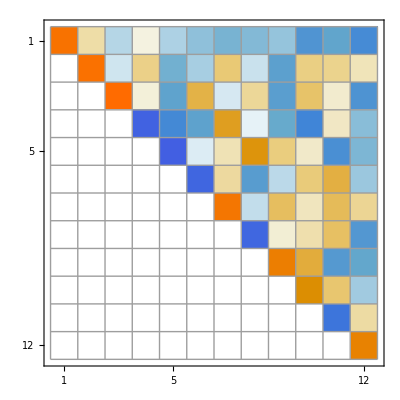

```mathematica
{m,n}={23,12};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A]; Q=Qᵀ;
Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R,A}]
MatrixPlot[R,Mesh->All]
```

### {Q_1,R_1}→Q_1.R_1=A→{Q_2,R_2}

The question now is how twitchy is the process.

```mathematica
{m,n}={52,25};
R1=UpperTriangularize[RandomReal[{-1,1},{n,n}]];
Q1=QRDecomposition[RandomReal[{-1,1},{m,n}]]⟦1⟧ᵀ;
A=Q1.R1; {Q2,R2}=QRDecomposition[A];Q2=Q2ᵀ;
TabView[{"R1"->MatrixPlot[R1,Mesh->All],"R2"->MatrixPlot[R2,Mesh->All]}];
TableForm[
Map[Norm,{A,A-Q1.R1,A-Q2.R2,Q1ᵀ.Q1-IdentityMatrix[n],Q2ᵀ.Q2-IdentityMatrix[n],R1-R2,Q1-Q2}],
TableHeadings->{{"||A||","res_1","res_2","orth_1","orth_2","||R1-R2||","||Q1-Q2||"}}]
```

||A|| | 4.07543
res_1 | 0.
res_2 | 3.99648×10^-15
orth_1 | 1.00863×10^-15
orth_2 | 1.29631×10^-15
||R1-R2|| | 1.93374×10^-12
||Q1-Q2|| | 2.26862×10^-11

What this means is that both the decompositions work but that they are not really all that similar! This means that the forward problem is ill-conditioned aka “twitchy”.  The product is stable but the products are not!
	As a bad analogy suppose I ask you to try to guess the numbers x and y from the product xy.

## Backward Stability of Householder QR

What we have is that multiplying the factors gives something close to the input.  In other words we have
	A→{Q,R}→Q̃.OverTilde[R=A+δA]
with δA relatively small.

Remember how our Householder computation went.  We started with a Tall-Skinny m×n matrix A_0 and computed a v_1 (using +, ×, √□, and ÷) that implicitly defined in exact arithmetic an exactly orthogonal Q_1=I_m-2 v_1⊗v_1which gave 
	A_1=Q_1.A_0
and all the arithmetic to make v_1 was to make A_1 have all the entries below the first exactly equal to zero.  Note, the condition number of Q_1 is as small as possible i.e. κ(Q_1)=1.  The condition number of (Q̃)_1 (the computed Q_1) is just a smidge bigger with κ((Q̃)_1)=1+ϵ_1with ϵ_1=O(ϵ_machine).  We continue with the next column and accumulate the product of all these Q_i until we are left with R. This finite sequence of actions are with matrices with condition number 1+O(ϵ_machine).  The result is a decomposition satisfying
	Q̃.R̃=A+δA  with (||δA||)/(||A||)=O(ϵ_machine)

## Combining Backward Stable Steps

If all steps of an algorithm are backwards stable then the algorithm is backward stable.

## A.x=b⟶Q.R.x=b⟶R.x=Qᵀ.b⟶x

Solving a linear system using the QR decomposition is backwards stable.

We know all the steps except the upper triangular linear solve are backwards stable.  We are going to look at the triangular solve (algorithm 17.1) right after we implement this

```mathematica
m=22;
x = RandomReal[{-1,1},m];
A=RandomReal[{-1,1},{m,m}];
b=A.x;
{Q,R}=QRDecomposition[A];Q=Qᵀ;
xHat=LinearSolve[R,Qᵀ.b];
Norm[x-xHat]
```

3.48134×10^-14

What we need to do is build a nearby problem that xHat solves exactly.  We are thinking of A as the data in Theorem 16.2 (in other words we can not mess with b right now) so we want to find a relatively small modification ΔA to A so that
	(A+ΔA).xHat=b
We know almost everything in this recipe except ΔA!  Rearrange to have
	ΔA.xHat=b-A.xHat
There are lots of possible choices! I can choose the rank one modification 
	ΔA=(b-A.xHat)⊗xHat/(||xHat||)
which has induced two norm ||ΔA||=||b-A.xHat||.

## Algorithm 17.1: R.x=b⟶x Manual To Start!

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!

```mathematica
Clear[x]
m=4;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
ans = Array[x,m];
b=RandomReal[{-1,1},m];
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
x[4]),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. The last row gives the last value in the answer!

```mathematica
ans⟦-1⟧=b⟦-1⟧/R⟦-1,-1⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last value in the answer the second last row gives the second last value in the answer.

```mathematica
ans⟦-2⟧=(b⟦-2⟧-R⟦-2,-1⟧*ans⟦-1⟧)/R⟦-2,-2⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last two values in the answer the third last row gives the third last value in the answer.

```mathematica
ans⟦-3⟧=(b⟦-3⟧-R⟦-3,-2;;-1⟧.ans⟦-2;;-1⟧)/R⟦-3,-3⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last three values in the answer the 4th last row gives the 4th last value in the answer.

```mathematica
ans⟦-4⟧=(b⟦-4⟧-R⟦-4,-3;;-1⟧.ans⟦-3;;-1⟧)/R⟦-4,-4⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(0.510183
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Looks as though we are done!  We should check we did not mess up!

```mathematica
R.ans-b
```

{1.11022×10^-16,1.11022×10^-16,0.,0.}

## Algorithm 17.1: R.x=b⟶x Script

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[x]
m=7;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
MatrixPlot[R,Mesh->All];
b=RandomReal[{-1,1},m];
ans=ConstantArray[0,m];
Do[
ans⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.ans⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}]
Norm[R.ans-b]
```

1.27192×10^-15

## Algorithm 17.1: R.x=b⟶x Function

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[AASUTSolve]
AASUTSolve[R_,b_]:= Module[{m=Length[b],x},
(* Alg 17.1 No checking *)
x=ConstantArray[0,m];
Do[
x⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.x⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}];
x]
```

Testing!

```mathematica
m=7;
R=UpperTriangularize[RandomReal[{0.1,10},{m,m}]];
b=RandomReal[{-1,1},m];
x=AASUTSolve[R,b];
Norm[R.x-b]
```

1.16441×10^-15